# G-Protein Activation

## Example of switching

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 13:43:47.331265 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

Reference:: figure 11.7 ,page 403 of G.Fain (1999) Molecular and Cellular Physiology of Neurons, Harvard University Press

xlr8r implementation
Created: 11 Aug 2005 BES
Revised: 15 Oct 07 BES Verify under M6.0

#### Define the network

```mathematica
gtpnet={
{R+L⇄RL, k1, k2},
{RL+αGDPβγ->RLαGDPβγ, k3},
{RLαGDPβγ->RLαβγ+GDP,k4},
{RLαβγ+GTP->RLαGTPβγ,k5},
{RLαGTPβγ->RL+αGTPβγ,k6},
{αGTPβγ->αGTP+βγ,k7},
{Overscript[X⇄activeX, αGTP], a8,d8,k8},{activeX->X, k12},
{Overscript[Y⇄activeY, βγ], a9, d9, k9},{activeY->Y, k13},
{αGTP->αGDP, k10},
{αGDP+βγ->αGDPβγ, k11}
};
```

#### Display the differential equations

```mathematica
interpret[gtpnet]//Reverse//Transpose//TableForm
```

activeX | activeX'[t]==-k12 activeX[t]+k8 Bind[X,αGTP][t]
activeY | activeY'[t]==-k13 activeY[t]+k9 Bind[Y,βγ][t]
GDP | GDP'[t]==k4 RLαGDPβγ[t]
GTP | GTP'[t]==-k5 GTP[t] RLαβγ[t]
L | L'[t]==-k1 L[t] R[t]+k2 RL[t]
R | R'[t]==-k1 L[t] R[t]+k2 RL[t]
RL | RL'[t]==k1 L[t] R[t]-k2 RL[t]+k6 RLαGTPβγ[t]-k3 RL[t] αGDPβγ[t]
RLαGDPβγ | RLαGDPβγ'[t]==-k4 RLαGDPβγ[t]+k3 RL[t] αGDPβγ[t]
RLαGTPβγ | RLαGTPβγ'[t]==-k6 RLαGTPβγ[t]+k5 GTP[t] RLαβγ[t]
RLαβγ | RLαβγ'[t]==k4 RLαGDPβγ[t]-k5 GTP[t] RLαβγ[t]
X | X'[t]==k12 activeX[t]-a8 X[t] αGTP[t]+d8 Bind[X,αGTP][t]
Y | Y'[t]==k13 activeY[t]-a9 Y[t] βγ[t]+d9 Bind[Y,βγ][t]
αGDP | αGDP'[t]==k10 αGTP[t]-k11 αGDP[t] βγ[t]
αGDPβγ | αGDPβγ'[t]==-k3 RL[t] αGDPβγ[t]+k11 αGDP[t] βγ[t]
αGTP | αGTP'[t]==-k10 αGTP[t]-a8 X[t] αGTP[t]+k7 αGTPβγ[t]+d8 Bind[X,αGTP][t]+k8 Bind[X,αGTP][t]
αGTPβγ | αGTPβγ'[t]==k6 RLαGTPβγ[t]-k7 αGTPβγ[t]
βγ | βγ'[t]==k7 αGTPβγ[t]-a9 Y[t] βγ[t]-k11 αGDP[t] βγ[t]+d9 Bind[Y,βγ][t]+k9 Bind[Y,βγ][t]
Bind[X,αGTP] | Bind[X,αGTP]'[t]==a8 X[t] αGTP[t]-d8 Bind[X,αGTP][t]-k8 Bind[X,αGTP][t]
Bind[Y,βγ] | Bind[Y,βγ]'[t]==a9 Y[t] βγ[t]-d9 Bind[Y,βγ][t]-k9 Bind[Y,βγ][t]

#### interpret the differential equaiton, freezing L and replacing it with a "pulse Train"

```mathematica
pulse[t_, time_,width_,magnitude_]:= 
If[t≥ time∧ t≤ time+width, magnitude, 0];
```

```mathematica
is=interpret[gtpnet,frozen-> {L}]/.{L[t]->pulse[t,30,25,1]+pulse[t,80,25,1]+pulse[t,130,25,1]}
```

{{activeX'[t]==-k12 activeX[t]+k8 Bind[X,αGTP][t],activeY'[t]==-k13 activeY[t]+k9 Bind[Y,βγ][t],GDP'[t]==k4 RLαGDPβγ[t],GTP'[t]==-k5 GTP[t] RLαβγ[t],L'[t]==0,R'[t]==-k1 (If[t≥30&&t≤55,1,0]+If[t≥80&&t≤105,1,0]+If[t≥130&&t≤155,1,0]) R[t]+k2 RL[t],RL'[t]==k1 (If[t≥30&&t≤55,1,0]+If[t≥80&&t≤105,1,0]+If[t≥130&&t≤155,1,0]) R[t]-k2 RL[t]+k6 RLαGTPβγ[t]-k3 RL[t] αGDPβγ[t],RLαGDPβγ'[t]==-k4 RLαGDPβγ[t]+k3 RL[t] αGDPβγ[t],RLαGTPβγ'[t]==-k6 RLαGTPβγ[t]+k5 GTP[t] RLαβγ[t],RLαβγ'[t]==k4 RLαGDPβγ[t]-k5 GTP[t] RLαβγ[t],X'[t]==k12 activeX[t]-a8 X[t] αGTP[t]+d8 Bind[X,αGTP][t],Y'[t]==k13 activeY[t]-a9 Y[t] βγ[t]+d9 Bind[Y,βγ][t],αGDP'[t]==k10 αGTP[t]-k11 αGDP[t] βγ[t],αGDPβγ'[t]==-k3 RL[t] αGDPβγ[t]+k11 αGDP[t] βγ[t],αGTP'[t]==-k10 αGTP[t]-a8 X[t] αGTP[t]+k7 αGTPβγ[t]+d8 Bind[X,αGTP][t]+k8 Bind[X,αGTP][t],αGTPβγ'[t]==k6 RLαGTPβγ[t]-k7 αGTPβγ[t],βγ'[t]==k7 αGTPβγ[t]-a9 Y[t] βγ[t]-k11 αGDP[t] βγ[t]+d9 Bind[Y,βγ][t]+k9 Bind[Y,βγ][t],Bind[X,αGTP]'[t]==a8 X[t] αGTP[t]-d8 Bind[X,αGTP][t]-k8 Bind[X,αGTP][t],Bind[Y,βγ]'[t]==a9 Y[t] βγ[t]-d9 Bind[Y,βγ][t]-k9 Bind[Y,βγ][t]},{activeX,activeY,GDP,GTP,L,R,RL,RLαGDPβγ,RLαGTPβγ,RLαβγ,X,Y,αGDP,αGDPβγ,αGTP,αGTPβγ,βγ,Bind[X,αGTP],Bind[Y,βγ]}}

#### predict a TIme course and plot the results using arbitray initial conditions and rate constants

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {activeX,activeY,RL,RLαGDPβγ,RLαGTPβγ,RLαβγ,αGDPβγ,αGTP,αGTPβγ,Bind[X,αGTP],Bind[Y,βγ]}

Warning:  The following symbols are undefined (and assumed to be equal to one (1)): {a8,a9,d8,d9,k1,k10,k11,k12,k13,k2,k3,k4,k5,k6,k7,k8,k9}

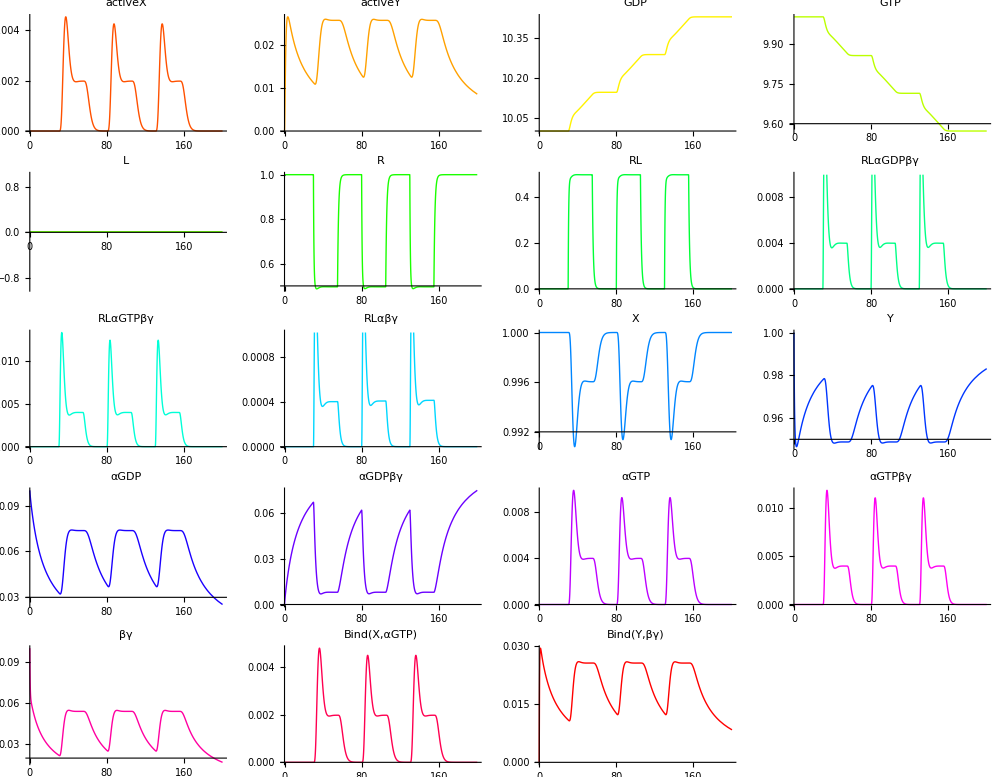

{{activeX→InterpolatingFunction[{{0.,200.}},<>],activeY→InterpolatingFunction[{{0.,200.}},<>],GDP→InterpolatingFunction[{{0.,200.}},<>],GTP→InterpolatingFunction[{{0.,200.}},<>],L→InterpolatingFunction[{{0.,200.}},<>],R→InterpolatingFunction[{{0.,200.}},<>],RL→InterpolatingFunction[{{0.,200.}},<>],RLαGDPβγ→InterpolatingFunction[{{0.,200.}},<>],RLαGTPβγ→InterpolatingFunction[{{0.,200.}},<>],RLαβγ→InterpolatingFunction[{{0.,200.}},<>],X→InterpolatingFunction[{{0.,200.}},<>],Y→InterpolatingFunction[{{0.,200.}},<>],αGDP→InterpolatingFunction[{{0.,200.}},<>],αGDPβγ→InterpolatingFunction[{{0.,200.}},<>],αGTP→InterpolatingFunction[{{0.,200.}},<>],αGTPβγ→InterpolatingFunction[{{0.,200.}},<>],βγ→InterpolatingFunction[{{0.,200.}},<>],Bind[X,αGTP]→InterpolatingFunction[{{0.,200.}},<>],Bind[Y,βγ]→InterpolatingFunction[{{0.,200.}},<>]}}

```mathematica
r=run[is,timeSpan-> 200,
initialConditions-> {X-> 1, Y-> 1, R-> 1, L-> 0.01, GDP-> 10, GTP-> 10,αGDP-> .1,βγ-> 0.1},
gridPlotVariables-> All,
plotVariables-> None, plot-> True, ImageSize-> 1000,
plotColumns-> 4]
```